Plate element for applications with Composite Laminates
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 22 November 2021 - Contact: m.marino@ing.uniroma2.it

## S1CLP - Plate Composite Laminate

- Based on the Classical Laminated Plate Theory (CLPT) with (x,y,z) local coordinate system and (X,Y,Z) global coordinate system
- Interpolation of local displacement field : in-plane u,v by Linear Lagrange  Polynomials; out-of-plane w Hermite shape functions (non-conforming: continuity of w, ∂w/∂x, ∂w/∂y)
- 12 element data: {pLoadX,pLoadY,pLoadZ, ex1,ex2,ex3, ey1,ey2,ey3, ez1,ez2,ez3, Rxx,Rxy,Rxz, Ryx, Ryy, Ryz}
	-- Input quantities (to be assigned BEFORE the simulation in AceFEM):
		pLoadX,pLoadY,pLoadZ : load vector in the global coordinate system 
		ex = ex1,ex2,ex3: unit vector identifying the first direction of the local basis written in the global coordinate system (the same for ey and ez) - ex, ey, ez are used for transforming global quantities in local quantities
	-- Output quantities (exported in the post-processing and read AFTER the simulation in AceFEM):
		Rx = Rxx, Rxy, Rxz : resultant of normal forces in local direction x
		Ry = Ryx, Ryy, Ryz : resultant of normal forces in local direction y

### Initialization

```mathematica
<<AceGen`;
SMSInitialize["S1CLP","Environment"-> "AceFEM","Mode"-> "Optimal"];
SMSTemplate["SMSTopology"->"S1",
(*Number of nodes*)
"SMSNoNodes"-> 4,
(*DOF for each node*)
"SMSDOFGlobal"-> {5,5,5,5},
(*ID of each node*)
"SMSNodeID"-> {"D","D","D", "D"},
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {
"A11 -A11","A12 -A12","A16 -A16","A22 -A22","A26 -A26","A66 -A66",
"B11 -B11","B12 -B12","B16 -B16","B22 -B22","B26 -B26","B66 -B66",
"D11 -D11","D12 -D12","D16 -D16","D22 -D22","D26 -D26","D66 -D66"}, "SMSDefaultData" -> {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},
(*Element data*)
"SMSNoElementData"->18
];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
nenX=4;
nenU=4;
ndim=SMSNoDimensions; 
ndimU=3;
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
)
```

### Element Definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
(*Read laminate stiffness properties in domain data*)
{A11,A12,A16,A22,A26,A66,B11,B12,B16,B22,B26,B66,D11,D12,D16,D22,D26,D66}⊨SMSIO["Domain data"];
(*Build the 𝔸𝔹𝔻 matrix*)
𝔸𝔹𝔻⊨{{A11,A12,A16,B11,B12,B16},{A12,A22,A26,B12,B22,B26},{A16,A26,A66,B16,B26,B66},{B11,B12,B16,D11,D12,D16},{B12,B22,B26,D12,D22,D26},{B16,B26,B66,D16,D26,D66}};

(*Read load vector in the 3D global coorindate system from Element data*)
𝕡Load⊨Table[SMSIO["Element data"[i]],{i,3}];

(*Integration points and weights*)
{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

(*Read all coordinates and degree of freedom*)
{𝕏IO,𝕡eIO}⊨SMSIO["All coordinates and DOFs"];
𝕡e=Flatten[𝕡eIO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
(*Lagrange shape functions for in-plane u and v*)
ℕhU⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nen}];
(*(Non-conforming) Hermite shape functions for w*)
ℕhw⊨Table[1/8(ξ Ξn⟦i,1⟧+1)(η Ξn⟦i,2⟧+1)(2+ξ Ξn⟦i,1⟧+η Ξn⟦i,2⟧-ξ^2-η^2),{i,1,nen}];
ℕhdwdξ⊨Table[1/8 Ξn⟦i,1⟧(ξ Ξn⟦i,1⟧+1)^2(ξ Ξn⟦i,1⟧-1)(η Ξn⟦i,2⟧+1),{i,1,nen}];
ℕhdwdη⊨Table[1/8 Ξn⟦i,2⟧(ξ Ξn⟦i,1⟧+1)(η Ξn⟦i,2⟧+1)^2(η Ξn⟦i,2⟧-1),{i,1,nen}];

(*GEOMETRIC MAPPING*)
𝕏IOG⊨𝕏IO⟦1;;nenX,1;;3⟧;
(* Compute element centroid in the global coordinate system*)
𝕏c⊨Sum[𝕏IOG⟦i,1;;3⟧,{i,4}]/4;
(*Read local basis from Element data*)
𝕖x⊨Table[SMSIO["Element data"[i]],{i,4,6}];
𝕖y⊨Table[SMSIO["Element data"[i]],{i,7,9}];
𝕖z⊨Table[SMSIO["Element data"[i]],{i,10,12}];
(*Calculate in-plane transformation matrix*)
𝕋2D⊨{𝕖x,𝕖y};
(*Transform the position vector of element nodes from the 3D global system (Xi,Yi,Zi) to a  2D local system (xi,yi) aligned with (ex,ey) and centered in element centroid *)
𝕏IOl⊨Table[𝕋2D.(𝕏IOG⟦i,1;;3⟧-𝕏c),{i,1,nenX}];
(*Position of the Ig Gauss point in the local coordinte system computed with a mapping based on Lagrange polynomials*)
𝕏l⊨SMSFreeze[ℕhU.𝕏IOl];
(*Compute Jacobian of the transformation*)
𝕁e⊨SMSD[𝕏l,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
(*Read global nodal displacement field unknowns Ui, Vi, Wi*)
𝕦IOG⊨𝕡eIO⟦1;;nenU,1;;3⟧; 
(*Transform nodal displacements from the 3D global system (Ui,Vi,Wi) to in-plane local displacements (ui,vi) aligned with (ex,ey) *)
𝕦IOl⊨Table[𝕋2D.𝕦IOG⟦i,1;;3⟧,{i,1,nenU}];
(*Compute in-plane displacement in Gauss-point by means of Lagrange shape functions*)
𝕦l⊨ℕhU.𝕦IOl;
(*Transform nodal displacements from the 3D global system (Ui,Vi,Wi) to out-of-plane local displacements (wi) aligned with ez *)
wIOl⊨Table[𝕖z.𝕦IOG⟦i,1;;3⟧,{i,1,nenU}]; 
(*Transform nodal unknowns of displacement gradient with respect to the 2D local system aligned with ex and ey (dwi/dx,dwi/dy) to displacement gradient with respect to the parent space (dwi/dξ, dwi/dη) *)
dwdxIO⊨𝕡eIO⟦1;;nenU,4⟧; 
dwdyIO⊨𝕡eIO⟦1;;nenU,5⟧; 
{dwdξIO,dwdηIO}⊨Transpose[Table[Transpose[SMSInverse[𝕁e]].{dwdxIO⟦i⟧,dwdyIO⟦i⟧},{i,nenU}]];
(*Compute out-of-plane displacement in Gauss-point by means of Hermite shape functions*)
wl⊨ℕhw.wIOl+ℕhdwdξ.dwdξIO+ℕhdwdη.dwdηIO;

(*Compute in-plane strain with respect to the 2D local system aligned with ex and ey*)
d𝕦d𝕏⊨SMSD[𝕦l,𝕏l,"Dependency"->{{ξ,η},𝕏l,SMSInverse[𝕁e]}];
{ϵox,ϵoy,γoxy}⊨{d𝕦d𝕏⟦1,1⟧,d𝕦d𝕏⟦2,2⟧,d𝕦d𝕏⟦1,2⟧+d𝕦d𝕏⟦2,1⟧};
(*Compute curvatures with respect to the 2D local system aligned with ex and ey*)
dwd𝕏⊨SMSD[wl,𝕏l,"Dependency"->{{ξ,η},𝕏l,SMSInverse[𝕁e]}];
ddwd𝕏2⊨SMSD[dwd𝕏,𝕏l,"Dependency"->{{ξ,η},𝕏l,SMSInverse[𝕁e]}];
{κx,κy,κxy}⊨{-ddwd𝕏2⟦1,1⟧,-ddwd𝕏2⟦2,2⟧,-2(ddwd𝕏2⟦1,2⟧+ddwd𝕏2⟦2,1⟧)/2};
ϵplate⊨{ϵox,ϵoy,γoxy,κx,κy,κxy};

(*ENERGY*)
(*Compute in-plane normal load (in the direction of ex and ey), positive if pointing in the direction of ex and ey*)
px⊨𝕡Load.𝕖x;
py⊨𝕡Load.𝕖y;
(*Compute out-of-plane normal load (in the direction of ez), positive if pointing inward (i.e., opposite to ez)*)
pz⊨-𝕡Load.𝕖z;
(*Compute total potential energy density*)
Ψe⊨1/2 ϵplate.𝔸𝔹𝔻.ϵplate-(𝕦l⟦1⟧px+𝕦l⟦2⟧py-wl pz);
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];

SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
```

```mathematica
SMSDo[
(*Compute residual vector*)
Rgi⊨Jed wgp SMSD[Ψe,𝕡e,i];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
(*Compute tangent element matrix*)
Kgij⊨ SMSD[Rgi,𝕡e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,1,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];

ℝx⫤{0,0,0};
ℝy⫤{0,0,0};

SMSDo[Ig,1,nip,1,{ℝx,ℝy}];

ElementDefinitions[Ig];
(*Compute generalized static quantities*)
{Nx,Ny,Nxy,Mx,My,Mxy}⊨𝔸𝔹𝔻.ϵplate;
(*Integrate σx within the element*)
ℝx⊣ℝx+wgp Jed Nx 𝕖x;
(*Integrate σy within the element*)
ℝy⊣ℝy+wgp Jed Ny 𝕖y;
 
(*Export of Gauss-point quantities*)
SMSIO[
{"ϵox"->ϵox,"ϵoy"->ϵoy,"γoxy"->γoxy, "dwdx"->dwd𝕏⟦1⟧, "dwdy"->dwd𝕏⟦2⟧,"κx"->κx,"κy"->κy,"κxy"->κxy,"ul"->𝕦l⟦1⟧,"vl"->𝕦l⟦2⟧,"wl"->wl,"Nx"->Nx,"Ny"->Ny,"Nxy"->Nxy,"Mx"->Mx,"My"->My,"Mxy"->Mxy}
,"Export to","Integration point post"[Ig]];

SMSEndDo[{ℝx,ℝy}];

(*Export of stress resultants in the 6 final entries of Element Data*)
SMSExport[Join[ℝx,ℝy],Table[ed$$["Data",i],{i,13,SMSNoElementData}]];

(*Export of nodal quantities*)
𝕦h⊨Transpose[𝕦IOG];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"DeformedMeshZ"->𝕦h⟦3⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧,"w"->𝕦h⟦3⟧},"Export to","Nodal point post"];
```

### Code generation

```mathematica
SMSWrite[];
```

File: S1CLP.c  Size: 79017  Time: 52
Method | SKR | SPP
No.Formulae | 860 | 461
No.Leafs | 16888 | 8470

## Material properties and ABD matrix

```mathematica
mixrules[Ef_,νf_,Gf_,Em_,νm_,Gm_,ff_]:=(
E1=(1-ff)Em+ff*Ef;
E2= 1/(((1-ff)/Em)-(ff/Ef));
ν12=νf*ff+νm*(1-ff);
G12=(((1-ff)/Gm)-(ff/Gf))^-1;
Print["E1: ",E1,"; E2: ",E2,"; ν12: ",ν12,"; G12: ",G12];
Return[{E1,E2,ν12,G12}]

);
(*E1=150;
E2=10;
ν12=0.3;
G12=5;
*)
(*{E1,E2,ν12,G12,DC}=mixrules[Ef,νf,Gf,Em,νm,Gm,ff];*)
{E1,E2,ν12,G12}=mixrules[200,0.35,25,5,0.37,2.2,0.56];
DC=1-ν12^2 E2/E1;
ℚ={{E1/DC,ν12 E2/DC,0},{ν12 E2/DC,E2/DC,0},{0,0,G12}};

𝕋σ[θ_]:={{Cos[θ]^2,Sin[θ]^2,2Cos[θ]Sin[θ]},{Sin[θ]^2,Cos[θ]^2,-2Cos[θ]Sin[θ]},{-Cos[θ]Sin[θ],Cos[θ]Sin[θ],Cos[θ]^2-Sin[θ]^2}};

(*Function written for a laminate made up by two layers*)
(*θv: collects angle of each layer*)
(*zv: collects heights of each layer*)
ABDcomp1[θv_,zv_,ℚ_]:=(
𝔸=DiagonalMatrix[{0,0,0}];
𝔹=DiagonalMatrix[{0,0,0}];
𝔻=DiagonalMatrix[{0,0,0}];

Do[
ℚbar=𝕋σ[θv⟦i⟧].ℚ⟦i⟧.Transpose[𝕋σ[θv⟦i⟧]];
𝔸=𝔸+ℚbar(zv⟦i+1⟧-zv⟦i⟧);
𝔹=𝔹+1/2(ℚbar(zv⟦i+1⟧^2-zv⟦i⟧^2));
𝔻=𝔻+1/3(ℚbar(zv⟦i+1⟧^3-zv⟦i⟧^3));
,{i,1,Length[θv]}];
Return[{𝔸,𝔹,𝔻}];
);
```

E1: 114.2; E2: 11.7371; ν12: 0.3588; G12: 5.63063

## FEM simulation: plate

### Definition of geometry, loads, parameters and mesh

```mathematica
(* definire una funzione per calcolare ℚ *)
(* aggiungere comando per regola miscele*)
Calcℚ[E1_,E2_,ν12_,G12_]:=(
DC=1-ν12^2 E2/E1;
ℚ={{E1/DC,ν12 E2/DC,0},{ν12 E2/DC,E2/DC,0},{0,0,G12}};
Return[ℚ];
);
Options[totalℚ]={"homogenlayer"->True};
totalℚ[var_,layer_,OptionsPattern[]]:=(
If[OptionValue["homogenlayer"]==True, 
ℚℚ=Table[DiagonalMatrix[{0,0,0}]*i,{i,1,var⟦1⟧}];
θθ=Table[DiagonalMatrix[{0,0,0}]*i,{i,1,var⟦1⟧}];
zzv=Table[0*i,{i,1,var⟦1⟧+1}];	
Do[
	θθ⟦j⟧=var⟦2⟧;
        zzv⟦j+1⟧=var⟦7⟧;
	ℚℚ⟦j⟧=Calcℚ[var⟦3⟧,var⟦4⟧,var⟦5⟧,var⟦6⟧]
	,{j,1,var⟦1⟧}];
Do[zzv⟦k⟧=zzv⟦k-1⟧+zzv⟦k⟧,{k,2,Length[zzv]}];
zzv=zzv-(Abs[zzv⟦1⟧-zzv⟦Length[zzv]⟧]/2);
Return[{ℚℚ,zzv,θθ}]
];

If[OptionValue["homogenlayer"]==False, 
(* METTI CALCOLO PER UTTI I LAYER DIVERSI CICLANDO SULLA DIMENSIONE DEI layer*)
index=0;
totalLayer=Total[Table[layer⟦i,1⟧,{i,1,Length[layer]}]];
ℚℚ=Table[DiagonalMatrix[{0,0,0}]*i,{i,1,totalLayer}];
θθ=Table[DiagonalMatrix[{0,0,0}]*i,{i,1,totalLayer}];
zzv=Table[0*i,{i,1,totalLayer+1}];
Do[
	Do[
	θθ⟦index+j⟧=layer⟦i,2⟧;
        zzv⟦index+j+1⟧=layer⟦i,7⟧;
	ℚℚ⟦index+j⟧=Calcℚ[layer⟦i,3⟧,layer⟦i,4⟧,layer⟦i,5⟧,layer⟦i,6⟧]
	,{j,1,layer⟦i,1⟧}];
index=layer⟦i,1⟧;
,{i,1,Length[layer]}];
 
Do[zzv⟦k⟧=zzv⟦k-1⟧+zzv⟦k⟧,{k,2,Length[zzv]}];
zzv=zzv-(Abs[zzv⟦1⟧-zzv⟦Length[zzv]⟧]/2);
Return[{ℚℚ,zzv,θθ}]
]

);
```

```mathematica
(* ciclo per calcolare Q a partire dal materiale specifico*)
layer={
(* n di layer, angolo, E1, E2, ν12,G12,spessore*)
{10,0,148,9.65,0.3,4.55,0.1},(*SOSTITUISCI VALORI*)
(*{10,45,16.39,16.39,0.801,38.19,0.1}*)
{10,45,148,9.65,0.3,4.55,0.1} (*SOSTITUISCI VALORI*)
}
(*PASSARE I VALORI DENTRO layer E LA VARIABILE A Falso 
per includere diversi strati
{ℚℚ,zzv,θθ}=totalℚ[0,layer,"homogenlayer"->False];
*)
strato={20,0,148,9.65,0.3,4.55,0.1}
(* OPPURE PASSARE VARIABILE True E LE PROPRIETà DELLO STRATO DENTRO strato
{ℚℚ,zzv,θθ}=totalℚ[strato,0,"homogenlayer"->True];*)
```

```mathematica
{ℚℚ,zzv,θθ}=totalℚ[0,layer,"homogenlayer"->False];
(*{ℚℚ,zzv,θθ}=totalℚ[strato,0,"homogenlayer"->True];*)
(*Plate L x H x h *)
L=10;
H=5;

t=L/10;
(*Surface normal load (positive if inward)*)
q3=0.02; (*force per unit area*)
(*Normal load applied on boundary at X=L (positive when aligned with global direction X)*)
q1=2 t; (* (force per unit area)*thickness = force per unit length *)
(*Laminate properties*)
(*
θv={0,0,90}Pi/180; (*angles with respect to global direction X*)
zv=Table[0*i,{i,1,Length[θv]+1}];
Do[
zv⟦i⟧=-t/2+(t*(i-1)/(Length[θv]));
,{i,1,Length[θv]+1}]
zv
(*
θv={0,0}Pi/180; (*angles with respect to global direction X*)
zv={-t/2,0,t/2};
*)*)
(*MatrixForm[ℚℚ]*)
{𝔸,𝔹,𝔻}=ABDcomp1[θθ*Pi/180,zzv,ℚℚ];
Print[{𝔸//MatrixForm,𝔹//MatrixForm,𝔻//MatrixForm}]
(*Mesh*)
raster=Table[{x,y,0},{y,0,H,H/10},{x,0,L,L/10}];
nmesh=20;
```

{(194.525 | 39.4633 | -34.7917
39.4633 | 55.3582 | -34.7917
-34.7917 | -34.7917 | 42.7391),(-51.6112 | 16.8196 | -17.3958
16.8196 | 17.9721 | -17.3958
-17.3958 | -17.3958 | 16.8196),(64.8416 | 13.1544 | -11.5972
13.1544 | 18.4527 | -11.5972
-11.5972 | -11.5972 | 14.2464)}

```mathematica
-
```

### Initialization FEM model

```mathematica
<<AceFEM`;

SMTInputData[];
SMTAddDomain["Ωc","S1CLP",{
"A11 *"-> 𝔸⟦1,1⟧,"A12 *"-> 𝔸⟦1,2⟧,"A16 *"-> 𝔸⟦1,3⟧,"A22 *"-> 𝔸⟦2,2⟧,"A26 *"-> 𝔸⟦2,3⟧,"A66 *"-> 𝔸⟦3,3⟧,
"B11 *"-> 𝔹⟦1,1⟧,"B12 *"->𝔹⟦1,2⟧,"B16 *"-> 𝔹⟦1,3⟧,"B22 *"-> 𝔹⟦2,2⟧,"B26 *"-> 𝔹⟦2,3⟧,"B66 *"-> 𝔹⟦3,3⟧,
"D11 *"-> 𝔻⟦1,1⟧,"D12 *"->𝔻⟦1,2⟧,"D16 *"->𝔻⟦1,3⟧,"D22 *"->𝔻⟦2,2⟧,"D26 *"->𝔻⟦2,3⟧,"D66 *"-> 𝔻⟦3,3⟧}];
SMTAddMesh[Raster[raster],"Ωc","S1",{nmesh,nmesh}];
(**)
SMTAddEssentialBoundary["X"==0&,1->0,2->0,3->0,4->0,5->0];
SMTAddNaturalBoundary["X"==L&,1->Line[{q1}]];
(**)

SMTAnalysis[];
(*SMTShowMesh["NodeMarks"->True,"BoundaryConditions"->True]
Intersection[SMTFindNodes["X"==L/2&],SMTFindNodes["Y"==H/2&]]*)
```

### Define local coordinate system and apply surface normal load p

```mathematica
(*Print Element Data of element 1*)
Print[SMTElementData[1,"Data"]];
(*Define entries of element data vectors with {qX,qY,qZ, ex1,ex2,ex3, ey1,ey2,ey3, ez1,ez2,ez3}*)
nel=SMTNoElements;
Do[
𝕖xi={1,0,0};
𝕖yi={0,1,0};
𝕖zi={0,0,1};
SMTElementData[i,"Data",Join[{0,0,-q3},𝕖xi,𝕖yi,𝕖zi,{0,0,0},{0,0,0}]];
,{i,1,nel}];
(*Print Element Data of element 1*)
Print[SMTElementData[1,"Data"]];
```

{0.,0.,-0.02,1.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.}

{0.,0.,-0.02,1.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.}

### Solution algorithm (fixed load-step, NR loop)

```mathematica
(*Direct Implementation*)


nstep=10;   Δλ=1/nstep;
qw1={{0,0}};
qw2={{0,0}};

Do[
SMTNextStep["Δλ"->Δλ];
λq=SMTData["Multiplier"];
While[
SMTConvergence[tolNR,maxNR]
,SMTNewtonIteration[];
];
,{i,1,nstep}];
```

Step/Iter=2/2 λ/Δλ=0.2/0.1 ∥Δp∥/∥R∥=2.13383×10^-12/1.48557×10^-12 Events=0 Status=0/{If[2>maxNR,MaxIterations,Null],If[2.13383×10^-12<tolNR,Convergence,Null]}

Divergence in iterative procedure.
Version: 7.303 MacOSX (3 Aug 21) (MMA 12.3) Module: SMTConvergence
See also: SMTConvergence  AceFEM Troubleshooting  Continue

$Aborted

### Post-processing

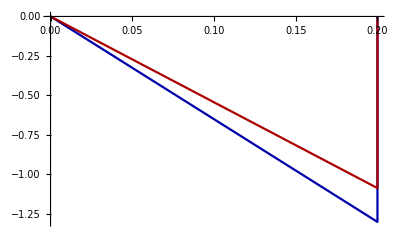

```mathematica
(*Store value of displacement w of points {L,H,0} and {0,H,0}*)
qw1=AppendTo[qw1,{λq,SMTPostData["wl",Point[{L,H,0}]]}];
qw2=AppendTo[qw2,{λq,SMTPostData["wl",Point[{L,0,0}]]}];(*Plot displacement w in p§oints {L,H,0} and {0,H,0}*)
ListLinePlot[{qw1,qw2},PlotStyle->{Darker[Blue],Darker[Red]}]
```

```mathematica
(*Preliminary call of post-processing routine*)
SMTPostData["u"];

(*Print Element Data of element 1*)
Print[SMTElementData[1,"Data"]]
```

0.

{0.,0.,-0.02,1.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.}

```mathematica
SMTPostData["ϵox",Point[{L/2,H/2,0}]] (*  for export *)
```

0.0133444

```mathematica
nel=SMTNoElements;
(*Print average normal stress in local direction x, σx*)
Print[Sum[SMTElementData[i,"Data"]⟦-6;;-4⟧,{i,1,nel}]/(L H)]
```

{2.,0.,0.}

```mathematica
(*Print total load*)
Print[{q1 H,0,-q3 L H}]
```

{10,0,-1.}

```mathematica
(*Compute Reaction force at boundary X=0*)
Reaction=Total[SMTResidual[Line[{{0,0,0},{0,H,0}}]]];
(*Print Reaction force at boundary X=0*)
Print[Reaction⟦1;;3⟧]
```

{-2.,4.44089×10^-16,1.}

## FEM simulation: cylinder

The plate element is used here to solve the problem of a cylinder under internal pressure. The use of S1CLP is correct only under the assumption of little initial curvature of the elements. Otherwise a shell element with initial curvature should be derived.

### Definition of geometry, loads, parameters and mesh

```mathematica
(*Cyliner L x R x h *)
L=10;
R=1;
t=R/5;
(*applied pressure*)
q=5; (*force per unit area*)
(*Laminate properties*)
θv={45,90,45}Pi/180; (*angles with respect to global direction X*)
zv=Table[0*i,{i,1,Length[θv]+1}];
Do[
zv⟦i⟧=-t/2+(t*(i-1)/(Length[θv]));
,{i,1,Length[θv]+1}]
zv
{𝔸,𝔹,𝔻}=ABDcomp[θv,zv,ℚ];
Print[{𝔸//MatrixForm,𝔹//MatrixForm,𝔻//MatrixForm}]
(*Mesh*)
raster1=Table[{x,R Cos[α],R Sin[α]},{α,0,Pi/2,Pi/20},{x,0,L,L/10}];
raster2=Table[{x,R Cos[α],R Sin[α]},{α,Pi/2,Pi,Pi/20},{x,0,L,L/10}];
raster3=Table[{x,R Cos[α],R Sin[α]},{α,Pi,2Pi,Pi/40},{x,0,L,L/10}];
nmesh=40;
```

{-1/10,-1/30,1/30,1/10}

{(3.78739 | 2.65124 | -2.34742
2.65124 | 13.1771 | -2.34742
-2.34742 | -2.34742 | 2.91549),(-0.20778 | -0.163336 | 0.156495
-0.163336 | -0.20778 | 0.156495
0.156495 | 0.156495 | -0.172144),(0.0152547 | 0.011871 | -0.0113024
0.011871 | 0.0187324 | -0.0113024
-0.0113024 | -0.0113024 | 0.0125561)}

### Initialization FEM model

```mathematica
<<AceFEM`;

SMTInputData[];
(*Geometry is created as the combination of 3 domains such that we have nodes {0,R,0}, {0,0,R} and {0,-R,0}, which is useful for applying boundary conditions to prevent rigid body motions*)
SMTAddDomain["Ωc1","S1CLP",{
"A11 *"-> 𝔸⟦1,1⟧,"A12 *"-> 𝔸⟦1,2⟧,"A16 *"-> 𝔸⟦1,3⟧,"A22 *"-> 𝔸⟦2,2⟧,"A26 *"-> 𝔸⟦2,3⟧,"A66 *"-> 𝔸⟦3,3⟧,
"B11 *"-> 𝔹⟦1,1⟧,"B12 *"->𝔹⟦1,2⟧,"B16 *"-> 𝔹⟦1,3⟧,"B22 *"-> 𝔹⟦2,2⟧,"B26 *"-> 𝔹⟦2,3⟧,"B66 *"-> 𝔹⟦3,3⟧,
"D11 *"-> 𝔻⟦1,1⟧,"D12 *"->𝔻⟦1,2⟧,"D16 *"->𝔻⟦1,3⟧,"D22 *"->𝔻⟦2,2⟧,"D26 *"->𝔻⟦2,3⟧,"D66 *"-> 𝔻⟦3,3⟧}];
SMTAddDomain["Ωc2","S1CLP",{
"A11 *"-> 𝔸⟦1,1⟧,"A12 *"-> 𝔸⟦1,2⟧,"A16 *"-> 𝔸⟦1,3⟧,"A22 *"-> 𝔸⟦2,2⟧,"A26 *"-> 𝔸⟦2,3⟧,"A66 *"-> 𝔸⟦3,3⟧,
"B11 *"-> 𝔹⟦1,1⟧,"B12 *"->𝔹⟦1,2⟧,"B16 *"-> 𝔹⟦1,3⟧,"B22 *"-> 𝔹⟦2,2⟧,"B26 *"-> 𝔹⟦2,3⟧,"B66 *"-> 𝔹⟦3,3⟧,
"D11 *"-> 𝔻⟦1,1⟧,"D12 *"->𝔻⟦1,2⟧,"D16 *"->𝔻⟦1,3⟧,"D22 *"->𝔻⟦2,2⟧,"D26 *"->𝔻⟦2,3⟧,"D66 *"-> 𝔻⟦3,3⟧}];
SMTAddDomain["Ωc3","S1CLP",{
"A11 *"-> 𝔸⟦1,1⟧,"A12 *"-> 𝔸⟦1,2⟧,"A16 *"-> 𝔸⟦1,3⟧,"A22 *"-> 𝔸⟦2,2⟧,"A26 *"-> 𝔸⟦2,3⟧,"A66 *"-> 𝔸⟦3,3⟧,
"B11 *"-> 𝔹⟦1,1⟧,"B12 *"->𝔹⟦1,2⟧,"B16 *"-> 𝔹⟦1,3⟧,"B22 *"-> 𝔹⟦2,2⟧,"B26 *"-> 𝔹⟦2,3⟧,"B66 *"-> 𝔹⟦3,3⟧,
"D11 *"-> 𝔻⟦1,1⟧,"D12 *"->𝔻⟦1,2⟧,"D16 *"->𝔻⟦1,3⟧,"D22 *"->𝔻⟦2,2⟧,"D26 *"->𝔻⟦2,3⟧,"D66 *"-> 𝔻⟦3,3⟧}];
SMTAddMesh[Raster[raster1],"Ωc1","S1",{nmesh,nmesh/2}];
SMTAddMesh[Raster[raster2],"Ωc2","S1",{nmesh,nmesh/2}];
SMTAddMesh[Raster[raster3],"Ωc3","S1",{nmesh,nmesh}];

(*Fix cylinder extremes*)
SMTAddEssentialBoundary["X"==0&,1->0,4->0];
SMTAddEssentialBoundary["X"==L&,1->0,4->0];
(*Prevent rigid-body motions*)
SMTAddEssentialBoundary["X"==0&&"Y"==R&&"Z"==0&,3->0];
SMTAddEssentialBoundary["X"==0&&"Y"==0&&"Z"==R&,2->0];
SMTAddEssentialBoundary["X"==0&&"Y"==-R&&"Z"==0&,3->0];

SMTAnalysis[];
```

### Define local coordinate system and apply internal pressure

```mathematica
nel=SMTNoElements;
Do[
Clear[Nodes]; Clear[Cent];
Nodes=SMTElementData[i,"Nodes"]⟦1;;4⟧;
Cent=Sum[SMTNodeData[Nodes⟦j⟧,"X"],{j,1,4}]/4;
αi=ArcTan[Cent⟦2⟧,Cent⟦3⟧];
𝕖xi={1,0,0};
𝕖zi=-{0,Cos[αi],Sin[αi]};
𝕖yi=Cross[𝕖zi,𝕖xi];
SMTElementData[i,"Data",Join[-q 𝕖zi,𝕖xi,𝕖yi,𝕖zi,{0,0,0},{0,0,0}]];
,{i,1,nel}];
```

### Solution algorithm (fixed load-step, NR loop)

```mathematica
(*Direct Implementation*)
tolNR=10^-8;maxNR=15;

nstep=10;   Δλ=1/nstep;
qw={{0,0}};

Do[
SMTNextStep["Δλ"->Δλ];
λq=SMTData["Multiplier"];
While[
SMTConvergence[tolNR,maxNR]
,SMTNewtonIteration[];
];
,{i,1,nstep}];
```

### Post - processing

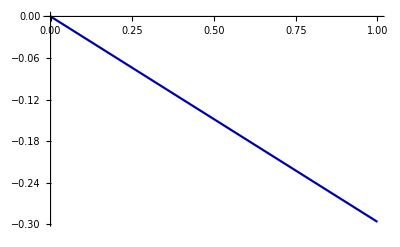

```mathematica
(*Store and Plot displacement wl of point {L/2,R,0}*)
qw=AppendTo[qw,{λq ,SMTPostData["wl",Point[{L/2,R,0}]]}];
ListLinePlot[qw,PlotStyle->{Darker[Blue]}]
```

```mathematica
(*Preliminary call of post-processing routine*)
SMTPostData["u"];
nel=SMTNoElements;
(*Print reaction load in X direcion applied at cylinder extremes (positive if traction)*)
Print[Reaction=Total[SMTResidual["X"==L&]]⟦1⟧]
```

2.39631

```mathematica
(*Print average circumferential stress*)
Fcirc=0;
Do[
Clear[Nodes]; Clear[Cent];
Nodes=SMTElementData[i,"Nodes"]⟦1;;4⟧;
Cent=Sum[SMTNodeData[Nodes⟦j⟧,"X"],{j,1,4}]/4;
αi=ArcTan[Cent⟦2⟧,Cent⟦3⟧];
𝕖xi={1,0,0};
𝕖zi={0,Cos[αi],Sin[αi]};
𝕖yi=Cross[𝕖zi,𝕖xi];
Fcirc=Fcirc+SMTElementData[i,"Data"]⟦-3;;-1⟧.(-𝕖yi);
,{i,1,nel}];
σcirc=Fcirc/(2 Pi R L t);
Print[σcirc]
Print[q R/t]
```

24.9742

25